## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[4];
```

## Utility Functions

The grid of x points in the region of the support of the potential

```mathematica
xgrid[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a,b,h}]//N;

Return[xs];
]
```

The grid of x points in the entire region including some to the left of the support of the potential for determining the value of T.

```mathematica
xgridFull[p_]:=Module[{a,b,n,m, h,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
h = p["h"];

xs = Table[x,{x,a-m*h,b,h}]//N;

Return[xs];
]
```

```mathematica
kGrid[p_]:=Module[{kmin,kmax,numk,kh},
kmin=p["kmin"];
kmax=p["kmax"];
numk = p["numk"];
kh = (kmax-kmin)/(numk-1);

Return[Table[k,{k,kmin,kmax,kh}]];
];
```

```mathematica
yvec[k_,p_]:=Module[{n,m, h,cDiffCoeffs,numNonzero, nonZeroElements},
n=p["n"];
m=p["m"];
h = p["h"];

cDiffCoeffs={1,-2,1};

nonZeroElements={
n+m->-cDiffCoeffs[[1]],
n+m+1->-1*(
cDiffCoeffs[[1]]*Exp[Sqrt[2]*I*k*h]+
cDiffCoeffs[[2]]+2*h^2*k^2)
};

Return[SparseArray[nonZeroElements,{n+m+1}]];
]
```

```mathematica
yvecKVec[kVec_,p_]:=Table[yvec[k,p],{k,kVec}]
```

```mathematica
D2Matrix[p_]:= Module[{n,m,cDiffCoeffs,bands},
n=p["n"];
m=p["m"];

cDiffCoeffs={1,-2,1};

bands=Table[Band[{1,i}]->cDiffCoeffs[[i]],{i,1,Length[cDiffCoeffs]}];

Return[SparseArray[bands,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrix[k_,p_]:=Module[{ n,m, h, band},
n=p["n"];
m=p["m"];
h = p["h"];

(*band = Band[{1,3}]->2*h^2*k^2;*)
band = Band[{1,2}]->2*h^2*k^2;
Return[SparseArray[band,{1+n+m, 1+n+m}]];
];
```

```mathematica
EMatrixKVec[kVec_,p_]:=Table[EMatrix[k,p],{k,kVec}]
```

```mathematica
VMatrix[V_,Vparams_,SEDict_]:=Module[{xg,n,m, h, u1V, matV},
xg=xgrid[SEDict][[2;;-1]];
n=SEDict["n"];
m=SEDict["m"];
h =SEDict["h"];

u1V=Band[{m+1,m+2}]->2*h^2*V[xg,Vparams];
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[matV];
];
```

## Solve Schrodinger equation

```mathematica
SchrEqOfV[V_,VParams_, SEDict_,kVec_,D2_,EMatrixVector_,yVector_]:=Module[{VV, soln},
VV = VMatrix[V,VParams, SEDict];

soln = Table[{
kVec[[i]],
LinearSolve[D2-VV+EMatrixVector[[i]], yVector[[i]],Method->"Banded"]
},{i,1, Length[kVec]}];
Return[soln];
];
```

```mathematica
TofV[k_,x1_,x2_,SEsol1_,SEsol2_]:=Module[{},
Exp[I*Sqrt[2]*k*x2]*(1-Exp[-I*2*Sqrt[2]*k*(x2-x1)])/
(SEsol2-SEsol1*Exp[-I*Sqrt[2]*k*(x2-x1)])
];
```

```mathematica
TofVVec[V_,VParams_, SEDict_,kVec_,D2_,EMatrixVector_,yVector_]:=
Module[{step,solk,xgf,x1,x2,Tk},
step=SEDict["TCalcStep"];
solk=SchrEqOfV[V,VParams,SEDict,kVec,D2,EMatrixVector,yVector];
xgf=xgridFull[SEDict];
x1=xgf[[1]];
x2=xgf[[step]];

Tk=Table[{
sol[[1]], 
TofV[sol[[1]],x1,x2, sol[[2,1]],sol[[2,step]]]
},
{sol,solk}];

Return[Tk];
]
```

## Define Cost Function

```mathematica
Cost[T_, TGoal_, SEDict_,weights_:Table[1,{i,1,Length[T_]}]]:=
Module[{temp,cost},

(*Calculate the cost function*)
cost = Sum[
weights[[i]]*(T[[i,2]]-TGoal[[i,2]])^2,
{i,1,Length[T]}] /
 Sum[weights[[i]],{i,1,Length[T]}] ;
Return[cost];
];
```

```mathematica
CostTemp[T_, TGoal_, SEDict_,weights_:Table[1,{i,1,Length[T_]}]]:=
Module[{temp,cost},
temp=SEDict["temp"];

(*Calculate the cost function*)
cost = Sum[weights[[i]]*Exp[-T[[i,1]]^2/(2*temp)]/(√(2 temp Pi))*(T[[i,2]]-TGoal[[i,2]])^2,
{i,1,Length[T]}]/
Sum[weights[[i]]*Exp[-T[[i,1]]^2/(2*temp)]/(√(2 temp Pi)),{i,1,Length[T]}] ;

Return[cost];
];
```

```mathematica
CostConstraint[ErrFunc_, Vpars_,SEDict_]:=Module[{alpha},
alpha=SEDict["alpha"];
alpha * ErrFunc[Vpars,SEDict]
]
```

## Search for the potential

```mathematica
BackgroundWeights[k_]:=Sqrt[Sinh[Pi Sqrt[2]k]^2/(Sinh[Pi Sqrt[2]k]^2+Cosh[Pi Sqrt[7]/2]^2)]
```

```mathematica
CustomStepMonitor[TGoal_,Vfunc_,Vpars_,SEDict_,kVec_ ,costFunction_,d2_,eMatrix_,yvec_,weights_:Table[1,{i,1,Length[TGoal_]}]]:=
Module[{tvec,cost,PlotA,PlotB},
tvec=TofVVec[Vfunc, Vpars,SEDict,kVec,d2,eMatrix,yvec];
cost=costFunction[Abs[tvec], TGoal, SEDict,weights];

(*ALERT: very bad programming!!!*)
If[cost≠lastCost,
Print["Cost: ", cost];
Print["Params: ",Vpars]; 

PlotA=Plot[Vfunc[x,Vpars],{x,SEDict["a"],SEDict["b"]},PlotRange->All];
PlotB=ListPlot[{TGoal,Abs[tvec]},PlotRange->All,PlotLabel->"Cost: "<>ToString[cost]];

Print[GraphicsRow[{PlotA,PlotB}, ImageSize->Large]]
];

lastCost=cost;
]
```

```mathematica
SearchPotential [
TGoal_,Vfunc_,Vpars_,parConstrs_,SEDict_,kVec_, costFunction_,errFunction_,
weights_:Table[1,{i,1,Length[TGoal_]}],
method_:{
"DifferentialEvolution", 
"Tolerance"->0.1,
"PostProcess"->False,
"PenaltyFunction"->Function[{d,i},d*10^(2)], 
"ScalingFactor"->0.75,
 "CrossProbability"->0.5,
"RandomSeed"->3
}
]:=
Module[{VparsFlat, soln,d2mat,emat,yyvec,lastCost},
VparsFlat=Flatten[Vpars];
d2mat = D2Matrix[SEDict];
emat=EMatrixKVec[kVec,SEDict];
yyvec=yvecKVec[kVec,SEDict];

lastCost=1000;

soln=NMinimize[{
Hold[
costFunction[Abs[TofVVec[Vfunc, Vpars,SEDict,kVec,d2mat,emat,yyvec]], TGoal,SEDict,weights]+
CostConstraint[errFunction, Vpars,SEDict]
],
parConstrs
},
VparsFlat, 
Method->method, 
AccuracyGoal->2,
PrecisionGoal->2,
MaxIterations->500,
StepMonitor:> Hold[Catch[CustomStepMonitor[TGoal, Vfunc,Vpars,SEDict,kVec,costFunction,d2mat,emat,yyvec,weights]]]
];

Return[soln];
]
```

## Define actual search parameters and potentials

```mathematica
VGauss[x_,params_]:=Module[{pot,A,x0,sigma},
A=params[[1]];
x0=params[[2]];
sigma=params[[3]];

pot = A*Exp[-(x-x0)^2/2/sigma];

Return[pot];
];
```

```mathematica
VGaussN[x_,params_]:=Module[{pot},
pot=Sum[VGauss[x,pars],{pars,params}];
Return[pot];
];
```

```mathematica
VGaussL2Err[params_,SEDict_]:=Module[{pot,A,x0,σ,a,b,Vout},
A=params[[1]];
x0=params[[2]];
σ=params[[3]];
a=SEDict["a"];
b=SEDict["b"];

Vout=√(π/2) A √σ (Erfc[(-a+x0)/(√2 √σ)]+Erfc[(b-x0)/(√2 √σ)]);

Return[Abs[Vout]^2];
];
```

```mathematica
VGaussL2ErrN[params_,SEDict_]:=Module[{pot},
pot=Sum[VGaussL2Err[pars,SEDict],{pars,params}];
Return[pot];
];
```

```mathematica
SEDict = Association["a"->-10, "b"->10,"n"->500,"m"->100,"kmin"->0.01,"kmax"->2.001,"numk"->100, "TCalcStep"->25, "temp"->0.5, "alpha"->10];
SEDict["h"]=(SEDict["b"]-SEDict["a"])/SEDict["n"];
kgrid = kGrid[SEDict];
```

```mathematica
VGaussL2ErrN[{{1,-2,1.5},{-2,5,3}},SEDict]
```

0.000285588

## “Low pass quantum filter”

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[0.5-k]},{k,kgrid}];
```

```mathematica
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}];
```

```mathematica
(*SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,sigma2>0.01,x01+x02==0, x02≥0},
SEDict,
kgrid,
weightsofKGoalCool]*)
```

## “High-pass quantum filter”

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[k-0.5]},{k,kgrid}];
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}];
```

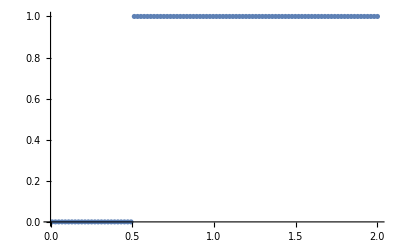

```mathematica
ListPlot[TofKGoalCool]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,sigma2>0.01,x01+x02==0, x02≥0},
SEDict,
kVecTest]*)
```

## “Low-pass quantum filter” 3 gaussians

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[-k+0.5]},{k,kgrid}];
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kgrid}]
```

{0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25}

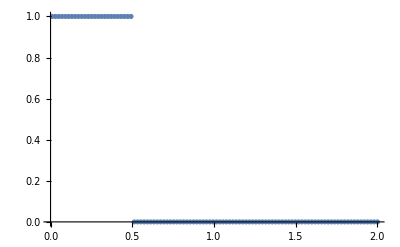

```mathematica
ListPlot[{TofKGoalCool}]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2},{A3,x03,sigma3}},
{sigma1>0.01,sigma2>0.01,sigma3>0.01,x01+x02+x03==0},
SEDict,
kVecTest,
weightsofKGoalCool]*)
```

## “k=0.5,1.5 double-comb” 4 gaussians, temp=infty

```mathematica
TofKGoalCool=Table[{k,
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/4]]]]+
KroneckerDelta[k,kgrid[[Round[Length[kgrid]*3/4]]]]},{k,kgrid}];
weightsofKGoalCool=Log[1+Table[(1+(Length[kgrid]-1)*(
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/4]]]]+
KroneckerDelta[k,kgrid[[Round[Length[kgrid]*3/4]]]]))+
BackgroundWeights[k],{k,kgrid}]]^2;
```

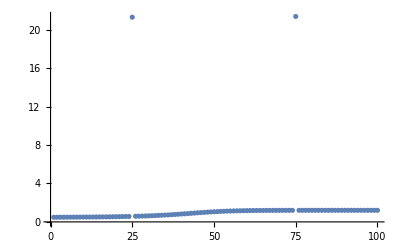

```mathematica
ListPlot[weightsofKGoalCool,PlotRange->All]
```

Cost: 0.376955

Params: {{0.860686,0.269306,0.692547},{0.968237,-0.227467,0.213694},{0.705134,-0.687143,1.5835},{0.478738,0.645304,1.42874}}

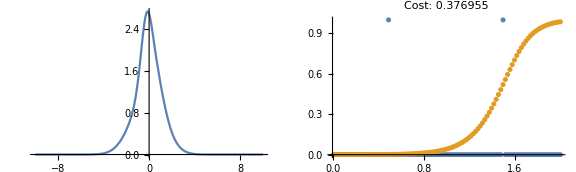

Cost: 0.318794

Params: {{1.27049,0.287372,0.774265},{2.02555,0.112244,0.464772},{1.26881,-0.349345,1.28381},{0.272641,-0.0502712,1.08021}}

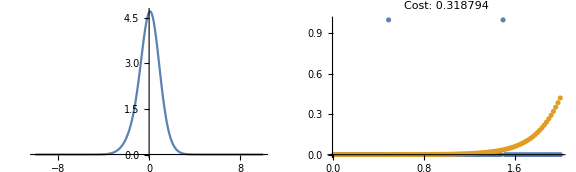

Cost: 0.318695

Params: {{0.826276,-0.377884,0.778012},{2.4323,-0.767826,0.821789},{-2.25572,1.63824,0.581024},{1.65875,-0.492529,1.52016}}

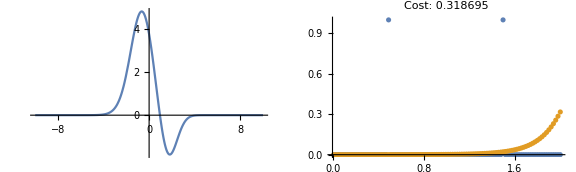

Cost: 0.303946

Params: {{-0.409168,-1.61999,0.404172},{4.44619,0.226707,0.101533},{1.10708,0.958427,3.48015},{0.706312,0.434855,1.3798}}

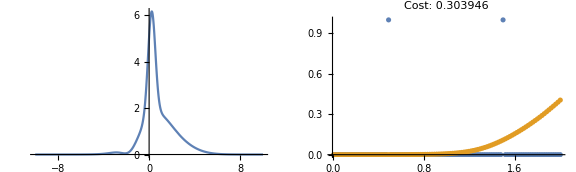

Cost: 0.290324

Params: {{-0.409168,-1.61127,1.36118},{4.44619,1.13999,0.101533},{-0.427493,0.0364286,3.48015},{0.706312,0.434855,1.3798}}

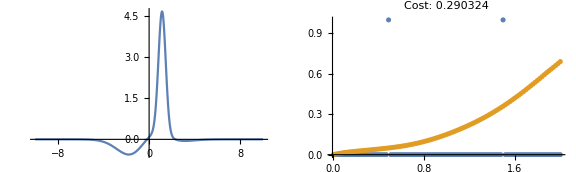

Cost: 0.282823

Params: {{-0.362742,-1.66277,0.564333},{5.65218,-2.26505,0.0555726},{-0.651674,-0.608108,0.910566},{0.624842,4.53593,0.126786}}

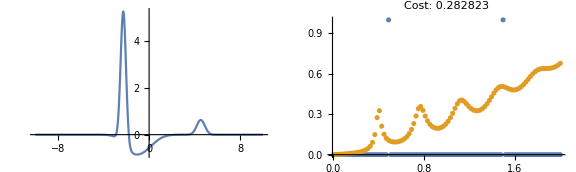

Cost: 0.271802

Params: {{2.3346,-2.29697,1.0226},{8.02799,-0.0110866,0.0751883},{1.49975,0.439742,0.417795},{-1.83214,1.86832,1.44398}}

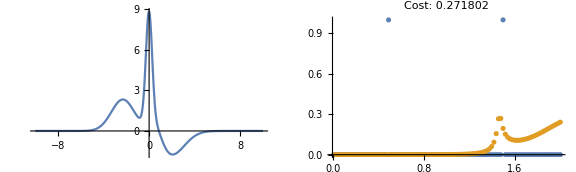

Cost: 0.269439

Params: {{4.27826,0.0875024,0.0567266},{3.07452,0.124954,0.017893},{-1.95461,-1.2893,2.30778},{-4.54078,1.07685,0.0129162}}

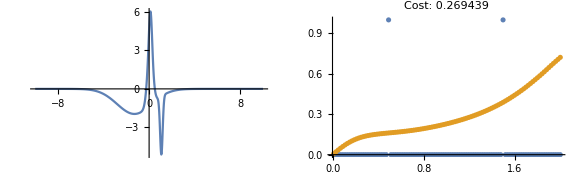

Cost: 0.263923

Params: {{-0.362742,2.849,1.39393},{5.65218,-2.26505,0.0555726},{-1.80672,-0.608108,1.22613},{0.624842,0.0241646,1.78863}}

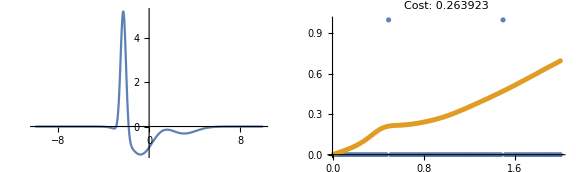

Cost: 0.229547

Params: {{-1.8201,-8.62449,0.0796806},{5.80345,2.43624,0.0379619},{1.08456,1.81572,0.567103},{2.3327,4.37253,0.652494}}

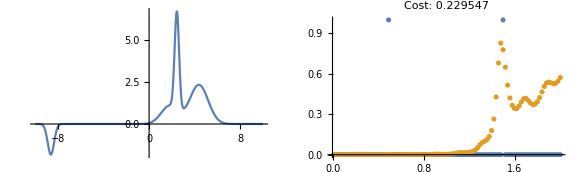

Cost: 0.223315

Params: {{0.873416,1.11665,0.576616},{5.49153,5.58768,0.0493402},{1.34201,0.244317,2.22177},{16.7943,-6.94865,0.0108692}}

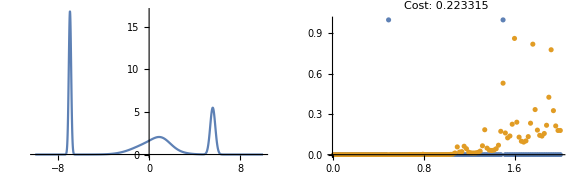

Cost: 0.212255

Params: {{-0.592132,3.33563,0.938235},{4.01794,3.94899,0.0677667},{-1.74296,0.338171,2.7412},{15.8037,-7.62279,0.0106126}}

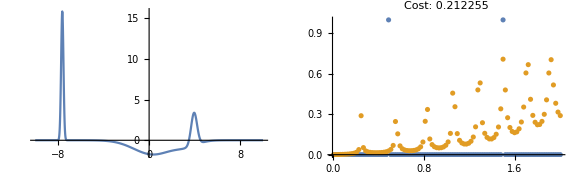

Cost: 0.208812

Params: {{-1.63682,1.10613,1.54148},{-2.29518,-2.17582,0.0102086},{-2.80484,0.576464,0.010008},{24.9907,0.49322,0.0100032}}

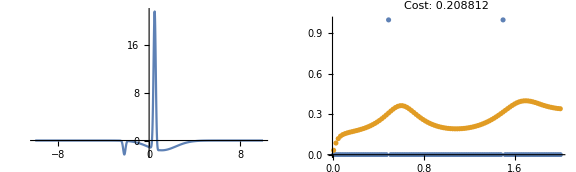

Cost: 0.126089

Params: {{0.696452,1.01881,0.0100035},{13.9582,1.11844,0.0302944},{2.5925,-1.61203,2.81438},{-3.90484,-0.525225,2.24074}}

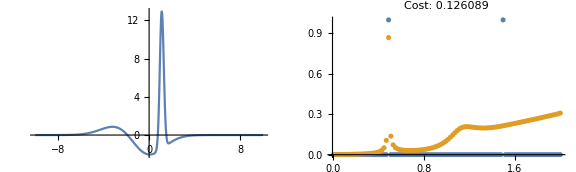

Cost: 0.105852

Params: {{-3.34818,2.14729,2.43141},{4.9586,-3.30247,0.027447},{-10.2271,-0.0740935,0.01},{17.8557,1.22927,0.01}}

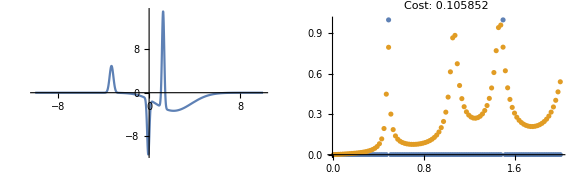

Cost: 0.105061

Params: {{-3.34818,2.14729,2.43141},{4.9586,-3.30247,0.027447},{-10.2271,-0.0740935,0.01},{17.9076,1.22927,0.01}}

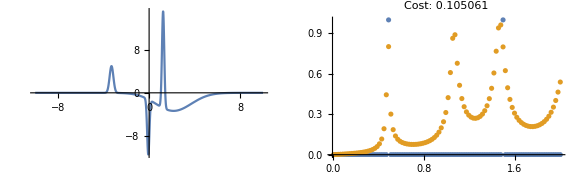

{0.105061,{A1→-3.34818,x01→2.14729,sigma1→2.43141,A2→4.9586,x02→-3.30247,sigma2→0.027447,A3→-10.2271,x03→-0.0740935,sigma3→0.01,A4→17.9076,x04→1.22927,sigma4→0.01}}

```mathematica
solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},
{A2,x02,sigma2},
{A3,x03,sigma3},
{A4,x04,sigma4}},
{sigma1>0.01,
sigma2>0.01, 
sigma3>0.01,
sigma4>0.01,
x01+x02+x03+x04==0},
SEDict,
kgrid,
Cost,
VGaussL2ErrN,
weightsofKGoalCool]
```

## “k=0.5,1.5 double-comb” 4 gaussians, temp=0.5

```mathematica
TofKGoalCool=Table[{k,
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/4]]]]+
KroneckerDelta[k,kgrid[[Round[Length[kgrid]*3/4]]]]},{k,kgrid}];
weightsofKGoalCool=Log[1+Table[(1+(Length[kgrid]-1)*(
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/4]]]]+
KroneckerDelta[k,kgrid[[Round[Length[kgrid]*3/4]]]]))+
BackgroundWeights[k],{k,kgrid}]]^2;
```

```mathematica
ListPlot[weightsofKGoalCool,PlotRange->All]
```

-Graphics-

```mathematica
(*solGaussNTemp=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},
{A2,x02,sigma2},
{A3,x03,sigma3},
{A4,x04,sigma4}},
{sigma1>0.01,
sigma2>0.01, 
sigma3>0.01,
sigma4>0.01,
x01+x02+x03+x04==0},
SEDict,
kgrid,
CostTemp,
weightsofKGoalCool]*)
```

## “k=1 single-comb” 2 gaussians, temp=infty

```mathematica
TofKGoalCool=Table[{k,
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/2]]]]},{k,kgrid}];
weightsofKGoalCool=Log[1+Table[(1+(Length[kgrid]-1)*(
KroneckerDelta[k,kgrid[[Round[Length[kgrid]/2]]]]))+
BackgroundWeights[k],{k,kgrid}]]^2;
```

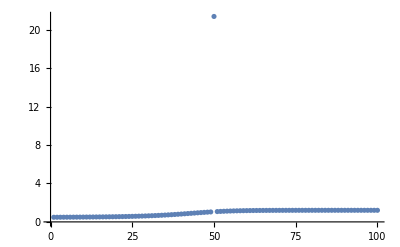

```mathematica
ListPlot[weightsofKGoalCool,PlotRange->All]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},
{A2,x02,sigma2}},
{sigma1>0.01,
sigma2>0.01, 
x01+x02==0
},
SEDict,
kgrid,
Cost,
VGaussL2ErrN,
weightsofKGoalCool]*)
```